```mathematica
SetDirectory[NotebookDirectory[]];
a0=Import["answer0.txt","Table"];
```

```mathematica
cs0 = x/.First@FindRoot[LegendreP[1/2,x]==0,{x,-0.5},WorkingPrecision->50]
dd=2.7142175397111330*(-0.5) * LegendreP[1/2,(-cs0)]/√(√(1-(Abs@cs0)^2))
```

-0.65222953196994067235474647720151281206818103290662

-1.34313

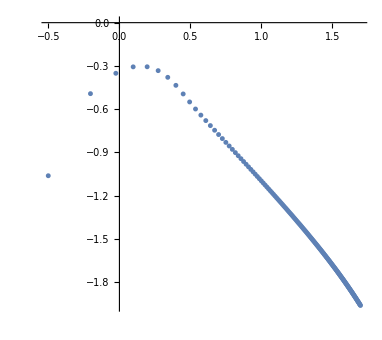

```mathematica
aa=Table[{a0⟦i,1⟧,Abs@a0⟦i,2⟧-Abs@dd*a0⟦i,1⟧^(1/2)},{i,2,Length@a0}];
ListPlot[Log10@Abs@%,AspectRatio->Automatic]
```

```mathematica
ArcCos@cs0
```

2.2813183068406470463924167927275591485937279252011